## Mitosis

## Model

We model the change in the distribution of the number i of mutations at a single locus in a population of diploids as a result of selection, mutation and reproduction by mitosis.

### Parameters

#### Genotype frequencies

x0, x1, and x2 represent the frequencies of the genotypes with 0, 1, and 2 mutations, respectively.

```mathematica
x={x0,x1,x2}
```

{x0,x1,x2}

#### Fitness

s < 0 is the deleterious effect of a mutation in a homozygous state.

```mathematica
w={1,1+s/2,1+s}
```

{1,1+s/2,1+s}

#### Mean fitness

Equation S2 (Supplementary Information)

```mathematica
w̄=Total[x w]
```

x0+(1+s/2) x1+(1+s) x2

### Evolution

#### Effect of selection

```mathematica
Δsel=(x w)/(w̄)-x
```

{-x0+x0/(x0+(1+s/2) x1+(1+s) x2),-x1+((1+s/2) x1)/(x0+(1+s/2) x1+(1+s) x2),-x2+((1+s) x2)/(x0+(1+s/2) x1+(1+s) x2)}

```mathematica
Total[Δsel/.{x2->1-x0-x1}]//Simplify
```

0

#### Effect of mutation

μ is the deleterious mutation rate.  We assume that (i) an individual can, at most, acquire one mutation, and (ii) mutations are irreversible.

```mathematica
Δmut={-2 μ x0,2 μ x0- μ x1,μ x1}
```

{-2 x0 μ,2 x0 μ-x1 μ,x1 μ}

```mathematica
Total[Δmut]
```

0

#### Effect of reproduction

Mitosis has no effect on genotype frequencies.

#### Combined effects of mutation, selection, and reproduction

Equation S1: genotype frequencies in the following generation

```mathematica
nextx=x+Δsel+Δmut//Simplify
```

{x0 (1/(x0+x1+(s x1)/2+x2+s x2)-2 μ),((2+s) x1)/(2 x0+(2+s) x1+2 (1+s) x2)+2 x0 μ-x1 μ,((1+s) x2)/(x0+x1+(s x1)/2+x2+s x2)+x1 μ}

```mathematica
Simplify[nextx=={ x0/(w̄)-2 μ x0,((2+s) x1)/(2 w̄)+2 μ x0- μ x1,((1+s) x2)/(w̄)+μ x1}]
```

True

## Equilibrium

### Equilibrium

There are three equilibria, but only the third equilibrium has x0 > 0

```mathematica
sol=Solve[nextx==x,{x0,x1,x2}]//FullSimplify
```

{{x0→0,x1→0,x2→1},{x0→0,x1→(s+2 μ+2 s μ)/(s+s μ),x2→-((2+s) μ)/(s (1+μ))},{x0→(s+2 (1+s) μ)^2/(s+2 s μ)^2,x1→-(4 μ (s+2 (1+s) μ))/(s+2 s μ)^2,x2→(4 μ^2)/(s+2 s μ)^2}}

Equation S3

```mathematica
eq=sol[[3]]//FullSimplify
```

{x0→(s+2 (1+s) μ)^2/(s+2 s μ)^2,x1→-(4 μ (s+2 (1+s) μ))/(s+2 s μ)^2,x2→(4 μ^2)/(s+2 s μ)^2}

### Stability

#### Jacobian matrix

```mathematica
f=nextx/.{x2->1-x0-x1}//FullSimplify
```

{x0 (-2/(-2+s (-2+2 x0+x1))-2 μ),-((2+s) x1)/(-2+s (-2+2 x0+x1))+2 x0 μ-x1 μ,(2 (1+s) (-1+x0+x1))/(-2+s (-2+2 x0+x1))+x1 μ}

Equation S4

```mathematica
j=({{D[f[[1]],x0], D[f[[1]],x1]}, {D[f[[2]],x0], D[f[[2]],x1]}})//Simplify
```

{{(4 s x0)/(-2+s (-2+2 x0+x1))^2-2/(-2+s (-2+2 x0+x1))-2 μ,(2 s x0)/(-2+s (-2+2 x0+x1))^2},{2 ((s (2+s) x1)/(-2+s (-2+2 x0+x1))^2+μ),(s (2+s) x1)/(-2+s (-2+2 x0+x1))^2-(2+s)/(-2+s (-2+2 x0+x1))-μ}}

```mathematica
Simplify[j=={{(4 s x0)/(-2+s (-2+2 x0+x1))^2+1/(w̄)-2 μ,(s x0)/(2(w̄)^2)},{(s (2+s) x1)/(2(w̄)^2)+2μ,(s (2+s) x1)/(4(w̄)^2)+(2+s)/(2 w̄)-μ}}/.{x2->1-x0-x1}]
```

True

#### Jacobian matrix evaluated at equilibrium

```mathematica
jeq=j/.eq//FullSimplify
```

{{((1+s) (s+4 s μ+4 (1+s) μ^2))/s,(s+2 (1+s) μ)^2/(2 s)},{-(2 (1+s) μ (s+2 (2+s) μ))/s,1/2 (2+s-2 μ-(4 (1+s) (2+s) μ^2)/s)}}

#### Eigenvalues of the Jacobian matrix

Equation S5

```mathematica
eig=Eigenvalues[jeq]//FullSimplify
```

{(1+s) (1+2 μ),1+μ+2 μ^2+1/2 s (1+2 μ)^2}

#### Stability condition

Equation S6

```mathematica
stab=Reduce[{-1<eig[[1]]<1,-1<eig[[2]]<1,0<μ<1,-1≤s<0}]
```

0<μ<1&&-1≤s<-(2 μ)/(1+2 μ)

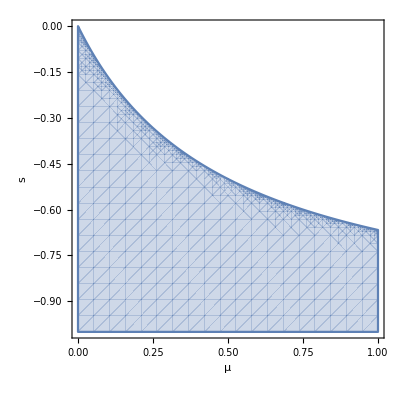

```mathematica
RegionPlot[stab,{μ,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

The equilibrium is also valid if the stability condition is met.

```mathematica
valid=Reduce[{0≤Values[eq[[1]]]≤1,0≤Values[eq[[2]]]≤1,0≤Values[eq[[3]]]≤1,0<μ<1,-1≤s<0}]
```

0<μ<1&&-1≤s≤-(2 μ)/(1+2 μ)

### Mean fitness at equilibrium (1 locus)

Equation S7

```mathematica
ŵ=w̄/.sol[[3]]//FullSimplify
```

1/(1+2 μ)

### Mean fitness at equilibrium (L loci)

If there are L fitness loci with the same μ and s, and there is linkage equilibrium between the loci, the mean fitness at equilibrium will be (ŵ)^L.  Taking a first-order Taylor expansion of ln((ŵ)^L) we get

```mathematica
Series[Log[(ŵ)^L],{μ,0,1}]
```

-2 L μ+O[μ]^2

Equation S8 and Equation 1 (main text)

U = 2 μ L is the deleterious mutation rate per diploid genome per generation.

```mathematica
Solve[Log[y^L]==-2 L μ,{y}]
```

{{y→ⅇ^(-2 μ)}}